# Fig 2

```mathematica
file="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\circles_data.hdf5";
data=Import[file, "Data"];
power = data["/power"];
freq = data["/freq"];
refl=data["/R_real"]+I data["/R_imag"];
```

{-15.,-10.,-5.,0.,5.,10.,15.}

```mathematica
powerRef=0;
npower=Length[power];
nfreq=Length[freq];
MinFreq=Min[freq];
MaxFreq=Max[freq];
MinPowerInd=2;
MaxPowerInd=npower-1
tofit=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,MinPowerInd,MaxPowerInd},{l,0,1},{j,1,nfreq}];
```

7

6

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{f0→6.54488,Γ→0.00180713,p→0.8099,α→6.76457×10^-7}

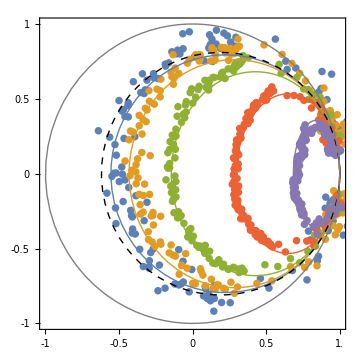

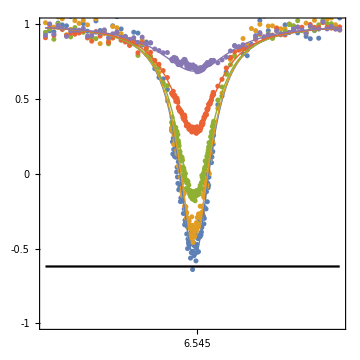

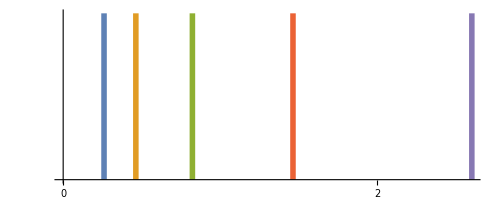

```mathematica
fit=FindFit[Flatten[tofit,2],(1-s)*Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α   P)]+s*Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α P)],{{f0,(freq[[1]]+freq[[-1]])/2},{Γ,0.00186},{p,0.793},{α,0.003}},{f,P,s}]
PlotIndices={1,2,3,4,5};
ΩRabi =10^3 √(α 10^((power[[MinPowerInd;;MaxPowerInd]]-powerRef)/10))/.fit;

g1=Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-1]],tofit[[i,2,;;,-1]]},{i,PlotIndices}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->PointSize[0.015]],
ParametricPlot[Evaluate@Table[{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]}/.fit,{i,PlotIndices}],{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Thick],
ParametricPlot[Evaluate@{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Black,Thick,Dashed]],
ParametricPlot[Evaluate@{Re[1-(2 Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2  Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Gray,Thick]]
,Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{{-1,-0.5,0,0.5,1.0},None}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]

g2=Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-4]],tofit[[i,1,;;,-1]]},{i,PlotIndices}],PlotStyle->PointSize[0.01],PlotRange->{{MinFreq,MaxFreq},{-1,1}}],Plot[Evaluate@Table[Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]/.fit,{i,PlotIndices}],{f,MinFreq,MaxFreq},PlotRange->All,PlotStyle->Thick],
Plot[1-2p/.fit,{f,MinFreq,MaxFreq},PlotStyle->Black],Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{Table[6.53+0.005i,{i,0,10}],None}},FrameTicksStyle->Directive[Black,16],AspectRatio->1,ImageSize->Medium]


g3=ParametricPlot[Evaluate[{#,x}&/@ΩRabi],{x,-0,0.5},PlotStyle->Thickness[0.01],Ticks->{Table[i,{i,0,10}],None},TicksStyle->Directive[Black,"Arial", 14]]
```

```mathematica
Export["circles.eps",g1]
```

# Fig 3

## Rabi

```mathematica
shiftfit2=FindFit[Transpose[{delays,Re[Rabirefl2[[;;Length@delays]]]+shift2}],A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B,{{A,0.3},B,{Ω,0.004},{ϕo,0},{TR,1000}},t]
p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{0.0,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]
scale2=1/avgRef2
scalefit2=FindFit[Transpose[{delays,Re[Rabirefl2[[;;Length@delays]]]*scale2}],A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B,{{A,0.3},B,{Ω,0.004},{ϕo,0},{TR,1000}},t]
p2=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]*scale2},PlotRange->{0.0,1.1}, PlotStyle->Orange, LabelStyle->Large,FrameLabel->{t[ns],Re[r]}],ListPlot[Transpose@{delays,Re[Refrefl2]*scale2},PlotRange->{-0.2,1.2}, PlotStyle->Blue],Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Blue],Plot[A*Cos[2π*Ω*t+ϕo]*Exp[-(t+ϕo)/TR]+B/.scalefit2,{t,0,delays[[-1]]}, PlotStyle->Orange, PlotRange->All],Plot[A*Exp[-t/TR]+B/.scalefit2,{t,0,delays[[-1]]}, PlotStyle->{Red, Dashed,Thick}, PlotRange->All], Plot[-A*Exp[-t/TR]+B/.scalefit2,{t,0,delays[[-1]]}, PlotStyle->{Red, Dashed,Thick}, PlotRange->All],Frame->True]
B2=B/.scalefit2;
A2=A/.scalefit2;
h=6.626*10^-34;
Teff=(h*1.006*10^9)/(-Log[(1-(B2-A2))/(1-(B2+A2))]*1.381*10^-23)

p2=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]*scale2},PlotRange->{0.0,1.1}, PlotStyle->Orange, LabelStyle->Large,FrameLabel->{t[ns],Re[r]}],Plot[A*Cos[2π*Ω*t+ϕo]*Exp[-(t+ϕo)/TR]+B/.scalefit2,{t,0,delays[[-1]]}, PlotStyle->Orange, PlotRange->All],Frame->True]
Pratio01=(1-(B2-A2))/(1-(B2+A2))
(1-(B2-A2))
(1-(B2+A2))
P0ini=0.64;
r0=0.658;
p2=Show[ListPlot[Transpose@{delays/1000,(1-Re[Rabirefl2]*scale2)*(P0ini/r0)},PlotRange->{0.0,1.0}, PlotStyle->Automatic, PlotMarkers->{"●"},LabelStyle->Large,FrameLabel->{t[μs],P0}],Plot[(1-(A*Cos[2π*Ω*1000*t+ϕo]*Exp[-(1000t+ϕo)/TR]+B))*(P0ini/r0)/.scalefit2,{t,0,delays[[-1]]/1000}, PlotStyle->Red, PlotRange->All],FrameTicks->{{Table[0.2i,{i,0,10}],None},{Table[0.2i,{i,0,10}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
Show[Plot[(1-(A*Cos[2π*Ω*1000*t+ϕo]*Exp[-(1000t+ϕo)/TR]+B))*(P0ini/r0)/.scalefit2,{t,0,delays[[-1]]/1000}, PlotStyle->Directive[Darker@RGBColor["#FF2414"],Thick],PlotRange->{0.1,.7}],ListPlot[Transpose@{delays/1000,(1-Re[Rabirefl2]*scale2)*(P0ini/r0)}, PlotStyle->{PointSize[0.02],RGBColor["#FF2414"]}],FrameTicks->{{Table[0.2i,{i,0,10}],None},{Table[0.2i,{i,0,10}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

## T1

```mathematica
model=A*Exp[-t/TR]+B;
model2=A1*Exp[-t/TR1+A2*(Exp[-t/TR2]-1)]+B;
data=Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}];
nmf=NonlinearModelFit[data,{model,BoundS},initguessS,t];
nmf2=NonlinearModelFit[data,{model2,BoundD},initguessD,t];
sparam=nmf["BestFitParameters"];
dparam=nmf2["BestFitParameters"];
nmf["ParameterConfidenceIntervalTable"]
nmf2["ParameterConfidenceIntervalTable"]
dataS=Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2/.sparam}];
Show[Plot[nmf[t]/.sparam,{t,0,delays[[-1]]},PlotStyle->{Red,Thick},PlotRange->All],ListPlot[dataS,PlotRange->All]]

Show[Plot[(1-(nmf[t*1000]/.sparam))*(P0ini/r0),{t,0,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#FF9D08"],Thick],PlotRange->{0.1,.7}],ListPlot[dataS,PlotStyle->Directive[PointSize[0.02],RGBColor["#FF9D08"]]],FrameTicks->{{Table[0.2i,{i,-5,5}],None},{Table[20i,{i,0,7}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

## T2